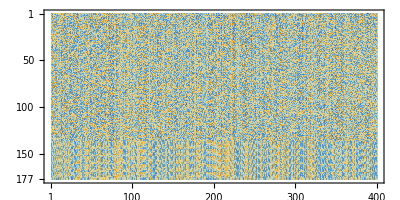

```mathematica
PartitionNest[{w_},n_]:={Transpose@Partition[w,n+1]};
PartitionNest[{w_,rest__},n_]:=Prepend[PartitionNest[{rest},Length[w]/(n+1)],Transpose@Partition[w,n+1]];
lists=Import["~/weightsCA2-2.tsv"];
matrices=PartitionNest[lists,176];
MatrixPlot[#,ImageSize->400]&/@matrices
```

```mathematica
matrices[[1]]//Dimensions
```

{11,24}

```mathematica
w=matrices;
```

```mathematica
Logistic[x_]:= 1/(1+Exp[-x])
sample[l_]:= Sign[Thread[l - RandomReal[1, Length[l]]]];
SampleHidden[w_][v_]:=sample[Logistic[wᵀ.v]];
SampleVisible[w_][h_]:= sample[Logistic[w.h]];
```

```mathematica
CreateTestVectorForRule[r_]:=StringJoin[ToString /@ Join[Flatten[CellularAutomaton[r,RandomInteger[1,8],16]],Flatten[Table["????????",{m,1,5}]]]];
```

```mathematica
Export["testvectors.txt",
CreateTestVectorForRule /@ {30,110,240}]
```

testvectors.txt

```mathematica
Do[
catest11=Join[Flatten[CellularAutomaton[30,RandomInteger[1,8],16]],Flatten[Table["????????",{m,1,5}]]]
catest12=Join[Flatten[CellularAutomaton[30,RandomInteger[1,8],16]],Flatten[Table[Table[1,{i,1,8}],{m,1,5}]]];
catest21=Join[Flatten[CellularAutomaton[154,RandomInteger[1,8],16]],Flatten[Table[IntegerDigits[0,2,8],{m,1,5}]]];
catest22=Join[Flatten[CellularAutomaton[154,RandomInteger[1,8],16]],Flatten[Table[Table[1,{i,1,8}],{m,1,5}]]];

catest={catest11,catest12,catest21,catest22};
data11=Append[2*#-1,1]&/@catest;
up1=SampleHidden[w[[1]]][#]&/@data11;
down1=SampleVisible[w[[1]]][#]&/@up1;
Final=Most[#1]&/@Map[((#+1)/2)&,down1];
{a,b,c,d}={Final[[1,-8;;-1]],Final[[2,-8;;-1]],Final[[3,-8;;-1]],Final[[4,-8;;-1]]};
Print[{a,b,c,d}]
,{loop,10}]
```

Set::write: Tag Times in {1, 0, 0, 0, 1, 1, 1, 0, 1, 1, 0, 1, 1, 0, 0, 0, 1, 0, 0, 1, 0, 1, 0, 1, 0, 1, 1, 1, 0, 1, 0, 1, 0, 1, 0, 0, 0, 1, 0, 1, 0, 1, 1, 0, 1, 1, 0, 1, 0, 1, « 91 »}\ {1, 1, 1, 1, 0, 0, 0, 0, 1, 0, 0, 0, 1, 0, 0, 1, 0, 1, 0, 1, 1, 1, 1, 1, 0, 1, 0, 1, 0, 0, 0, 0, 1, 1, 0, 1, 1, 0, 0, 0, 1, 0, 0, 1, 0, 1, 0, 1, 0, 1, « 126 »} is Protected.

{{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{0,0,0,0,0,0,0,1},{1,1,1,1,1,1,1,1}}

Set::write: Tag Times in {1, 1, 0, 1, 0, 1, 1, 0, 1, 0, 0, 1, 0, 1, 0, 0, 1, 1, 1, 1, 0, 1, 1, 1, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 1, 1, 1, 0, 0, 0, 0, 1, 1, 0, 0, 1, 1, 0, « 91 »}\ {1, 1, 1, 1, 0, 0, 0, 0, 1, 0, 0, 0, 1, 0, 0, 1, 0, 1, 0, 1, 1, 1, 1, 1, 0, 1, 0, 1, 0, 0, 0, 0, 1, 1, 0, 1, 1, 0, 0, 0, 1, 0, 0, 1, 0, 1, 0, 1, 0, 1, « 126 »} is Protected.

{{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1}}

Set::write: Tag Times in {1, 1, 1, 1, 0, 1, 0, 0, 1, 0, 0, 0, 0, 1, 1, 1, 0, 1, 0, 0, 1, 1, 0, 0, 1, 1, 1, 1, 1, 0, 1, 0, 1, 0, 0, 0, 0, 0, 1, 0, 1, 1, 0, 0, 0, 1, 1, 0, 1, 0, « 91 »}\ {1, 1, 1, 1, 0, 0, 0, 0, 1, 0, 0, 0, 1, 0, 0, 1, 0, 1, 0, 1, 1, 1, 1, 1, 0, 1, 0, 1, 0, 0, 0, 0, 1, 1, 0, 1, 1, 0, 0, 0, 1, 0, 0, 1, 0, 1, 0, 1, 0, 1, « 126 »} is Protected.

General::stop: Further output of Set :: write will be suppressed during this calculation.

{{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,0}}

{{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{0,0,0,0,0,0,0,1},{1,1,1,1,1,1,1,1}}

{{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1}}

{{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1}}

{{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1}}

«1 more identical outputs»

{{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{0,0,0,0,0,0,0,1},{1,1,1,1,1,1,1,1}}

{{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1}}